# General Polyhedron -Graphics- |z_1⟩ =|z_1⟩ |ω_1⟩ =|ω_1⟩ |z_2⟩ = |z_2⟩ |ω_2⟩ = |ω_2⟩ ... ... |z_(N-1)⟩ = |z_(N-1)⟩ |ω_(N-1)⟩ = |ω_(N-1)⟩ |z_N⟩ = |z_N⟩ |ω_N⟩ =|ω_N⟩

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/enekoaranguren/Documents/lqg

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

```mathematica
messageHandler=If[Last[#],Interrupt[]]&;
Internal`AddHandler["Message",messageHandler];
```

## Main

```mathematica
evolution[parameters_]:=Module[{array=parameters},
{γ,H0,λ}={array[["γ"]], array[["H0"]],array[["λ"]]};
{tmin,tmax}={array[["tmin"]],array[["tmax"]]};
 {n}={array[["edges"]]};
{ndsolvemethod}={array[["method"]]};
{facenormals}={array[["facenormals"]]};

{z,ω}={List[],List[]};
For[i=1,i≤ n,i++,
z=Append[z,{Symbol["z"<>ToString@i<>ToString@1],Symbol["z"<>ToString@i<>ToString@2]}];
ω=Append[ω,{Symbol["ω"<>ToString@i<>ToString@1],Symbol["ω"<>ToString@i<>ToString@2]}]];

Matrices;
Eα[t_]=Table[z[[i,1]][t]* z[[j,1]][t]+z[[i,2]][t]* z[[j,2]][t],{i,1,n},{j,1,n}];
Fα[t_]=Table[-z[[j,1]][t] z[[i,2]][t]+z[[j,2]][t]z[[i,1]][t],{i,1,n},{j,1,n}];
Fcα[t_]=Fα[t]*;
Eβ[t_]=Table[ω[[i,1]][t]* ω[[j,1]][t]+ω[[i,2]][t]* ω[[j,2]][t],{i,1,n},{j,1,n}];
Fβ[t_]=Table[-ω[[j,1]][t] ω[[i,2]][t]+ω[[j,2]][t]ω[[i,1]][t],{i,1,n},{j,1,n}];
Fcβ[t_]=Fβ[t]*;

Solve differential equations;
{eqz0,eqz1,eqω0,eqω1}={List[],List[],List[],List[]};
{soluz0,soluz1,soluω0,soluω1}={List[],List[],List[],List[]};
For[i=1,i≤ n,i++,
		eqz0=Append[eqz0,z[[i,1]]'[t]==Sum[-ⅈ λ[[i,l]] Eβ[t][[i,l]] z[[l,1]][t]-2 ⅈ γ[[i,l]]* Fcβ[t][[i,l]]z[[l,2]][t]*,{l,1,n}]];
		eqz1=Append[eqz1,z[[i,2]]'[t]==Sum[-ⅈ λ[[i,l]] Eβ[t][[i,l]] z[[l,2]][t]+2 ⅈ γ[[i,l]]* Fcβ[t][[i,l]]z[[l,1]][t]*,{l,1,n}]];
		eqω0=Append[eqω0,ω[[i,1]]'[t]==Sum[-ⅈ λ[[i,l]] Eα[t][[i,l]] ω[[l,1]][t]-2 ⅈ γ[[i,l]]* Fcα[t][[i,l]]ω[[l,2]][t]*,{l,1,n}]];
		eqω1=Append[eqω1,ω[[i,2]]'[t]==Sum[-ⅈ λ[[i,l]] Eα[t][[i,l]] ω[[l,2]][t]+2 ⅈ γ[[i,l]]* Fcα[t][[i,l]]ω[[l,1]][t]*,{l,1,n}]]];

z0vec=Table[z[[i,1]][0]==z0[[i,1]],{i,1,n}];
z1vec=Table[z[[i,2]][0]==z0[[i,2]],{i,1,n}];
ω0vec=Table[ω[[i,1]][0]==ω0[[i,1]],{i,1,n}];
ω1vec=Table[ω[[i,2]][0]==ω0[[i,2]],{i,1,n}];
initialconditions=Join[z0vec,z1vec,ω0vec, ω1vec];

For[i=1,i≤n,i++,
times={};
soluz0=Append[soluz0,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, z[[i,1]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",PrecisionGoal-> ∞]];
soluz1=Append[soluz1,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, z[[i,2]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",PrecisionGoal-> ∞]];
soluω0=Append[soluω0,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, ω[[i,1]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",PrecisionGoal-> ∞]];
soluω1=Append[soluω1,NDSolve[{eqz0,eqz1,eqω0,eqω1,initialconditions}, ω[[i,2]],{t, tmin,tmax},Method-> ndsolvemethod/._Missing-> "Automatic",StepMonitor:>AppendTo[times,t],PrecisionGoal-> ∞]];
];

times = Sort[times];
times = Range[tmin, tmax, (tmax-tmin)/100];

solutions=Flatten[{soluz0,soluz1,soluω0,soluω1}];

Hamiltonian;
e[t_]= ∑_(i=1)^n (∑_(j=1)^n λ[[i,j]]Eα[t][[i,j]]Eβ[t][[i,j]]);
f[t_]=  ∑_(i=1)^n (∑_(j=1)^n γ[[i,j]] Fα[t][[i,j]]Fβ[t][[i,j]]);
fc[t_]=∑_(i=1)^n (∑_(j=1)^n γ[[i,j]]*Fcα[t][[i,j]]Fcβ[t][[i,j]]);
H[t_]= e[t]+f[t]+fc[t];

Closure Constraint;
closurez1[t_]=Sum[Abs[z[[i,1]][t]]^2-Abs[z[[i,2]][t]]^2,{i,1,n}];
closurez2[t_]=Sum[z[[i,1]][t] z[[i,2]][t]*,{i,1,n}];
closureω1[t_]=Sum[Abs[ω[[i,1]][t]]^2-Abs[ω[[i,2]][t]]^2,{i,1,n}];
closureω2[t_]=Sum[ω[[i,1]][t] ω[[i,2]][t]*,{i,1,n}];

Quadrupole;
σ[1]={{0,1},{1,0}};
σ[2]={{0,-ⅈ},{ⅈ,0}};
σ[3]={{1,0},{0,-1}};

zz[t_]=List[];
For[i=1,i≤ n,i++,
	zz[t_]=Append[zz[t],{z[[i,1]][t],z[[i,2]][t]}]];

quadrupole[t_,a_,b_]=1/2 Sum[((zz[t][[k]]*.σ[a].zz[t][[k]]) (zz[t][[k]]*.σ[b]. zz[t][[k]]))/(zz[t][[k]]*.zz[t][[k]]),{k,n}];

T[t_]=Re[{{quadrupole[t,1,1],quadrupole[t,1,2],quadrupole[t,1,3]},
	     {quadrupole[t,2,1],quadrupole[t,2,2],quadrupole[t,2,3]},
	     {quadrupole[t,3,1],quadrupole[t,3,2],quadrupole[t,3,3]}}];
(*
MaximumT={{NMaximize[{Evaluate[quadrupole[t,1,1]/.solutions],tmin<t<tmax},t][[1]],
		  NMaximize[{Evaluate[quadrupole[t,1,2]/.solutions],tmin<t<tmax},t][[1]],
		  NMaximize[{Evaluate[quadrupole[t,1,3]/.solutions],tmin<t<tmax},t][[1]]},
		 {NMaximize[{Evaluate[quadrupole[t,2,1]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,2,2]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,2,3]/.solutions],tmin<t<tmax},t][[1]]},
		 {NMaximize[{Evaluate[quadrupole[t,3,1]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,3,2]/.solutions],tmin<t<tmax},t][[1]],
		 NMaximize[{Evaluate[quadrupole[t,3,3]/.solutions],tmin<t<tmax},t][[1]]}};
maxquad=Re[Max[MaximumT]];
*)

area[t_]=Re[quadrupole[t,1,1]+quadrupole[t,2,2]+quadrupole[t,3,3]];
(*
{a0[t_],b0[t_],c0[t_]}={quadrupole[t,1,1],quadrupole[t,2,2],quadrupole[t,1,2]};

eigenvalues[t_]=Re[{1/2((a0[t]+b0[t])+Sqrt[a0[t]^2+b0[t]^2-2a0[t] b0[t]+4c0[t]^2]),
			      1/2((a0[t]+b0[t])-Sqrt[a0[t]^2+b0[t]^2-2a0[t] b0[t]+4c0[t]^2]),
			      quadrupole[t,3,3]}/.solutions];
eigenvectors[t_]={Normalize[{1,-1/c0[t](a0[t]-eigenvalues[t][[1]]),0}],
				Normalize[{1,-1/c0[t](a0[t]-eigenvalues[t][[2]]),0}],
				{0,0,1}}/.solutions;
*)

eigenvalues[t_]:=Eigenvalues[T[t]];

Volume;
nor[t_,a_]:=1/2{zz[t][[a]]*.σ[1].zz[t][[a]],zz[t][[a]]*.σ[2].zz[t][[a]],zz[t][[a]]*.σ[3].zz[t][[a]]};

volume = {};
volume2 = {};
previouscentroid = None;
For[tstep=1, tstep≤Length[times], tstep++,

normals ={};
For[i=1, i≤ n, i++,
normals = Append[normals, Re[nor[times[[tstep]],i]/.solutions]]];

Export["normals.txt",ExportString[Flatten[Re[normals]],"PythonExpression"]];
RunProcess[{"Python", "reconstruction.py"}];

vertices = Import["vertices.csv","CSV"];
faces =  DeleteCases[IntegerPart[Import["faces.csv","CSV"]],0,2];
volume = Append[volume,{times[[tstep]],Import["volume.csv", "CSV"][[1,1]]}];

If[facenormals=="Yes",
facescoords=ConstantArray [{},Length[faces]];
For[ii=1,ii≤ Length[faces],ii++,
For[jj=1,jj≤ Length[faces[[ii]]],jj++,
AppendTo[facescoords[[ii]],vertices[[faces[[ii,jj]]]]]
 ]];

facesgeomcenter={};
origin = Mean[vertices];
For[ii=1,ii≤ Length[faces],ii++,

stCoords=facescoords[[ii]][[Last@FindShortestTour[facescoords[[ii]]]]];

If[Polygon[facescoords[[ii]]]//RegionQ,

AppendTo[facesgeomcenter,RegionCentroid[Polygon[stCoords]]],

AppendTo[facesgeomcenter,previouscentroid[[ii]]+(origin-previousorigin)]];
];
previousorigin = Mean[vertices];
previouscentroid = facesgeomcenter;

poli = Graphics3D[{Opacity[0.75],Polyhedron[vertices,faces],Black, Opacity[0.7],Table[Arrow[{facesgeomcenter[[ii]],facesgeomcenter[[ii]]+normals[[ii]]}],{ii,1,Length[faces]}]},Boxed->False],
poli = Graphics3D[{Opacity[0.75],Polyhedron[vertices,faces]},Boxed->False]
];

Export["pics/"<> IntegerString[tstep,10,4]<>".png",poli,ImageResolution->100];

(* COMPROBAMOS CON EL CÓDIGO DEL TETRAEDRO *)
If[n==4,
volume2=Append[volume2,{times[[tstep]],Sqrt[2/9  Abs[Dot[nor[times[[tstep]],1],Cross[nor[times[[tstep]],2],nor[times[[tstep]],3]]]]]/.solutions}];
u=9/2 volume2[[tstep]][[2]]^2;

ad =Sqrt[2/u]Cross[nor[times[[tstep]],2],nor[times[[tstep]],3]]/.solutions;
ab =Sqrt[2/u]Cross[nor[times[[tstep]],3],nor[times[[tstep]],4]]/.solutions;
ac =Sqrt[2/u]Cross[nor[times[[tstep]],4],nor[times[[tstep]],2]]/.solutions;

d=3/4 ad-1/4 ab-1/4 ac;
c=2/3 ac-1/3 d-1/3 ab;
b=1/2(-c-d+ab);
a=-b-c-d;

datavertices={a,b,c,d};

poli2 = Graphics3D[{Opacity[.75],Tetrahedron[{datavertices}]},Boxed->False];
Export["pics2/"<> IntegerString[tstep,10,4]<>".png",poli2,ImageResolution->100]];

Run["rm vertices.csv"];
Run["rm faces.csv"];
Run["rm volume.csv"];

];
volume3[t_] = 4/3 π eigenvalues[t][[1]] eigenvalues[t][[2]] eigenvalues[t][[3]];

(*
Plots;

Spinors;
plotz=Join[Table[Abs[z[[i,1]][t]/.solutions],{i,1,n}],
		    Table[Abs[z[[i,2]][t]/.solutions],{i,1,n}]];
zlabel=Join[Table[MaTeX["|z_{"<>ToString@i<>"1}|"],{i,1,n}],
		      Table[MaTeX["|z_{"<>ToString@i<>"2}|"],{i,1,n}]];
plotω=Join[Table[Abs[ω[[i,1]][t]/.solutions],{i,1,n}],
		    Table[Abs[ω[[i,2]][t]/.solutions],{i,1,n}]];
ωlabel=Join[Table[MaTeX["|\\omega_{"<>ToString@i<>"1}|"],{i,1,n}],
		      Table[MaTeX["|\\omega_{"<>ToString@i<>"2}|"],{i,1,n}]];

gr1 =Plot[{plotz}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None}, AxesOrigin-> {0,0},PlotLegends-> Placed[{zlabel}, Above],PlotStyle -> {Thickness[0.004],Dashed}];
gr11 =Plot[{plotω}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None},AxesOrigin-> {0,0},PlotLegends-> Placed[{ωlabel}, Above],PlotStyle -> {Thickness[0.004],Dashed}];

Area;
totalareaz=1/2 Sum[Abs[z[[i,1]][t]/.solutions]^2+Abs[z[[i,2]][t]/.solutions]^2,{i,1,n}];
individualareaz=1/2 Table[Abs[z[[i,1]][t]/.solutions]^2+Abs[z[[i,2]][t]/.solutions]^2,{i,1,n}];
labelareaz=Table[MaTeX["X_"<>ToString@i],{i,1,n}];
totalareaω=1/2 Sum[Abs[ω[[i,1]][t]/.solutions]^2+Abs[ω[[i,2]][t]/.solutions]^2,{i,1,n}];
individualareaω=1/2 Table[Abs[ω[[i,1]][t]/.solutions]^2+Abs[ω[[i,2]][t]/.solutions]^2,{i,1,n}];
labelareaω=Table[MaTeX["Y_"<>ToString@i],{i,1,n}];

gr2 = Plot[{totalareaz,individualareaz}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None},AxesOrigin-> {0,0},PlotLegends-> Placed[Flatten[{MaTeX["\\sum_{i} X_{i}"],labelareaz}],Above],PlotRange-> All];
gr12 = Plot[{totalareaω,individualareaω}, {t,tmin,tmax},AxesLabel-> {MaTeX["t"],None},AxesOrigin-> {0,0},PlotLegends-> Placed[Flatten[{MaTeX["\\sum_{i} Y_{i}"],labelareaω}],Above],PlotRange-> All];

Closure;
gr3 = Plot[{Abs[closurez1[t]/.solutions],
		 Abs[closurez2[t]/.solutions],
		 Abs[closureω1[t]/.solutions],
		 Abs[closureω2[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\text{Closure1 }z"],MaTeX["\\text{Closure2 }z"],
																			MaTeX["\\text{Closure1 }\\omega"],MaTeX["\\text{Closure2 }\\omega"]}, Above],PlotRange-> {-0.01,0.01},AxesLabel-> {MaTeX["t"],None}, PlotStyle -> {Blue,Darker[Green], Directive[Red,Dashed],Directive[Brown,Dashed]}];

Hamiltonian;
gr4= Plot[{Re[e[t]/.solutions],
		Im[e[t]/.solutions],
		Abs[e[t]/.solutions]},{t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(e)"], MaTeX["\\operatorname{Im}(e)"], MaTeX["\\operatorname{Abs}(e)"]},Above],
												 PlotStyle -> {Blue, Red,  Darker[Green]},AxesLabel-> {MaTeX["t"],None}];
gr5=Plot[{Re[f[t]/.solutions],
		Im[f[t]/.solutions],
		Abs[f[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(f)"], MaTeX["\\operatorname{Im}(f)"], MaTeX["\\operatorname{Abs}(f)"]},Above],
														  PlotStyle -> {Blue, Red,  Darker[Green]},AxesLabel-> {MaTeX["t"],None}];
gr6=Plot[{Re[fc[t]/.solutions],
		Im[fc[t]/.solutions],
		Abs[fc[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(f^{*})"],MaTeX["\\operatorname{Im}(f^{*})"], MaTeX["\\operatorname{Abs}(f^{*})"]},Above],
															PlotStyle -> {Blue, Red, Darker[Green]},AxesLabel-> {MaTeX["t"],None}];
gr7=Plot[{Re[H[t]/.solutions],
		Im[H[t]/.solutions],
		Abs[H[t]/.solutions]}, {t,tmin,tmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(H)"], MaTeX["\\operatorname{Im}(H)"], MaTeX["\\operatorname{Abs}(H)"]},Above],
														PlotRange-> All,PlotStyle -> {Blue, Red, Darker[Green]},AxesLabel-> {MaTeX["t"],None}];

Quadrupole;
gr8 = Show[GraphicsGrid[Table[Plot[Abs[quadrupole[t,i,j]/.solutions],{t,tmin,tmax},PlotRange-> {0,maxquad},AxesLabel-> {MaTeX["t"],None}],{i,3},{j,3}]],PlotLabel->MaTeX["\\text{Quadrupole}"]];
gr9 = Plot[{totalareaz,totalareaω,area[t]/.solutions},{t,tmin,tmax},AxesOrigin-> {0,0},PlotLegends-> Placed[{MaTeX["E_z"],MaTeX["E_\\omega"], MaTeX["\\operatorname{Tr}[Q]"]},Above],PlotRange-> All,PlotStyle -> {Blue, Directive[Darker[Green],Dashed],Directive[Red,Dotted]},AxesLabel-> {MaTeX["t"],None}];
gr10=Plot[{eigenvalues[t][[1]],eigenvalues[t][[2]],eigenvalues[t][[3]]},{t,tmin,tmax},AxesOrigin-> {0,0},PlotStyle -> {Darker[Green],Blue, Red},
	PlotLegends-> Placed[{MaTeX["Q_{1}"], MaTeX["Q_{2}"],MaTeX["Q_{3}"]},Above],AxesLabel-> {MaTeX["t"],None}];

*)

Volume;
gr13=ListLinePlot[{volume},PlotRange-> {0,All},PlotLabel->MaTeX["\\text{Volume}"],AxesLabel-> {MaTeX["t"],None}];
(*
gr14=ListLinePlot[{volume2},PlotRange-> {0,All},PlotLabel->MaTeX["\\text{Volume}"],AxesLabel-> {MaTeX["t"],None}];
*)
gr15 = Plot[{volume3[t]/.solutions},{t,tmin,tmax}];

Return;
<|(*"spinorsz"-> gr1,"Ez"-> gr2,"closure"-> gr3 ,"e"-> gr4, "f"-> gr5, "fc"-> gr6, "H"-> gr7,
  "quad"-> gr8, "checkareas"-> gr9,"eigenvalues"-> gr10,"spinorsω"-> gr11,"Eω"-> gr12, *)"volume"-> gr13(*, "volume2"-> gr14*),"volume3"-> gr15|>

];
```

## Build Initial System

```mathematica
initialvalues[parameters_]:=Module[{array=parameters},
{γ,H0,λ}={array[["γ"]], array[["H0"]],array[["λ"]]};
 {n}={array[["edges"]]};
{ndsolvemethod,save}={array[["method"]],array[["save"]]};

SeedRandom[Method -> "MersenneTwister"];
	points = {};
	For[i = 1, i≤ n , i++,
	u = RandomReal[{0, 1}];
	v = RandomReal[{0, 1}];
	θ= 2 π u;
	ϕ = ArcCos[2 v-1];
	points=Append[points,{Sin[ϕ] Cos[θ],Sin[ϕ] Sin[θ],Cos[ϕ]}]];

weight=RandomVariate[NormalDistribution[0,1/Sqrt[2]],n];
For[i=1,i≤ n,i++,
points[[i]] = points[[i]] weight[[i]]];

z0={};
For [i=1,i≤ n,i++,
phase=ArcTan[points[[i,2]]/points[[i,1]]];
z0=Append[z0,{ Sqrt[(Norm[points[[i]]]+points[[i,3]])/2],ⅇ^(-ⅈ phase) Sqrt[(Norm[points[[i]]]-points[[i,3]])/2]}]];

X11=Sum[Abs[z0[[i,1]]]^2,{i,1,n}];
X12=Sum[z0[[i,1]] z0[[i,2]]*,{i,1,n}];
X22=Sum[Abs[z0[[i,2]]]^2,{i,1,n}];

randomchoice=RandomInteger[{1,4}];
 Λcomp=NSolve[{X11==(X11 X22 -X12 X12*)(α α* + β β*),
		      X12==(X11 X22 -X12 X12*) (α η* + β δ*),
		      X12*==(X11 X22 -X12 X12*) (α* η + β* δ),
		      X22==(X11 X22 -X12 X12*)(η η*+ δ δ*),
		      α==α*,
		      β==η*,
		      β*==η,
		      δ==δ*},{α,β,η,δ,α*,β*,η*,δ*},Complexes][[randomchoice]];

Λ={{Λcomp[[1,2]],Λcomp[[2,2]]},
     {Λcomp[[3,2]],Λcomp[[4,2]]}};

For [i=1,i≤n,i++,
	z0[[i]]=Inverse[Λ].z0[[i]]];

randomizedlabels=RandomSample[Range[1,n]];

eq1=zi0'[t]==-ⅈ (zj0[t]* zi0[t] + zj1[t]* zi1[t]) zj0[t];
eq2=zi1'[t]==-ⅈ (zj0[t]* zi0[t] + zj1[t]* zi1[t]) zj1[t];
eq3=zj0'[t]==-ⅈ (zi0[t]* zj0[t] + zi1[t]* zj1[t]) zi0[t];
eq4=zj1'[t]==-ⅈ (zi0[t]* zj0[t] + zi1[t]* zj1[t]) zi1[t];

ω0=z0;
For[i=1,i≤ n,i++,
	If[i≠n,j=i+1,j=1];

	randomtime=RandomReal[{0,100}];
	{coordi,coordj}={randomizedlabels[[i]],randomizedlabels[[j]]};

	initialspinors={zi0[0]==ω0[[coordi,1]], zi1[0]==ω0[[coordi,2]], zj0[0]== ω0[[coordj,1]], zj1[0]==ω0[[coordj,2]]};
	soluzi0=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zi0,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	soluzi1=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zi1,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	soluzj0=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zj0,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	soluzj1=NDSolve[{eq1,eq2, eq3, eq4,initialspinors}, zj1,{t, 0, randomtime},Method-> ndsolvemethod/._Missing-> "Automatic"];
	solutions0=Flatten[{soluzi0,soluzi1,soluzj0,soluzj1}];

	ω0[[coordi,1]]=zi0[randomtime]/.solutions0;
	ω0[[coordi,2]]=zi1[randomtime]/.solutions0;
	ω0[[coordj,1]]=zj0[randomtime]/.solutions0;
	ω0[[coordj,2]]=zj1[randomtime]/.solutions0;

	Clear[zi0,zi1,zj0,zj1,soluzi0,soluzi1,soluzj0,soluzj1,solutions0]];


If[save=="Yes",
folder=DateString[Now,{"Day","-","Month","-","Year"}];
file=DateString[Now,{"Hour",".", "Minute",".","Second"}];
foldername="plots/"<>folder<>"/";
filename=foldername<>file<>".mx";

initialdata=<|"edges"-> n,"H0"-> H0,"γ"-> γ,"λ"-> λ,"z0"-> z0,"ω0"-> ω0|>;

With[{dirname=foldername},
	Switch[FileType[dirname],
			None,CreateDirectory[dirname]]];
Export[filename,initialdata],None];
Print[filename];
<|"z0"-> z0, "ω0"-> ω0,"Λ"-> Λ|>
];
```

## Print Plots

```mathematica
plot[parameters_]:=Module[{array=parameters},
params=array;

If[ToString[params[["initialdata"]]]=="None",
ini=initialvalues[params];
{params[["z0"]],params[["ω0"]]}={ini[["z0"]],ini[["ω0"]]},

ini=Import["plots/"<>params[["initialdata"]]<>".mx"];
{z0,ω0}={ini[["z0"]],ini[["ω0"]]};
{params[["λ"]],params[["γ"]],params[["edges"]],params[["H0"]]}={ini[["λ"]],ini[["γ"]] ,ini[["edges"]],ini[["H0"]]}];

allplots=evolution[params];
(*
Print[MaTeX["\\text{\\Huge{Spinors}}"]];
Print[""];
Print[Style[Row[{allplots[["spinorsz"]],allplots[["Ez"]],allplots[["spinorsω"]],allplots[["Eω"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{\\Huge{Quadrupole and Volume}}"]];
Print[""];
Print[Style[Row[{allplots[["quad"]],allplots[["eigenvalues"]],allplots[["volume"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{\\Huge{Consistency Checks}}"]];
Print[Style[Row[{allplots[["closure"]],allplots[["H"]],allplots[["checkareas"]]}], ImageSizeMultipliers->{1,1}]];
*)

Print[MaTeX["\\text{\\Huge{Volume}}"]];
Print[""];
Print[Style[Row[{allplots[["volume"]],allplots[["volume3"]]}], ImageSizeMultipliers->{1,1}]];

(*
Print[MaTeX["\\text{\\Huge{Volume 2}}"]];
Print[""];
Print[Style[Row[{allplots[["volume2"]]}], ImageSizeMultipliers->{1,1}]];
*)
];
```

## Input

filename

-Graphics-

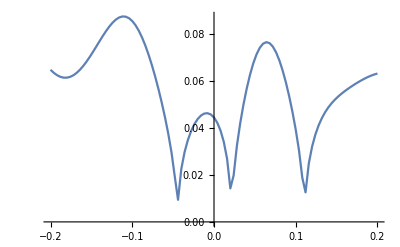
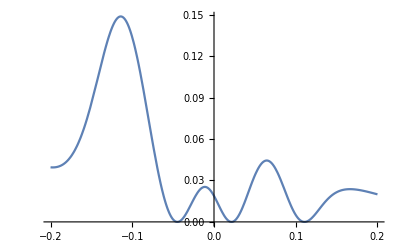

```mathematica
n=5;
λ = ConstantArray[5,{n,n}];
γ = ConstantArray[2,{n,n}];

{tmin,tmax}={-0.2,0.2};
initialdata = "02-01-2022/19.26.51";
initialdata = "04-01-2022/10.14.08";
initialdata = "None";

params=<|"tmin"-> tmin, "tmax"-> tmax,
	      "γ"-> γ,"H0"-> 0,"λ"->λ,
	      "edges"-> n,"initialdata"-> initialdata,
	      "method"-> "Automatic","save"-> "No","facenormals"->"No"|>;

plot[params]
```

```mathematica
(*
n=7;

λ = ConstantArray[0,{n,n}];
For[i=1,i≤ n, i++,
For[j=i,j≤n, j++,
λ[[i,j]] = Input["λ[["<>ToString@i<>","<>ToString@j<>"]]"];

If[Head[λ[[i,j]]]=== Real || Head[λ[[i,j]]]=== Integer,
λ[[j,i]] = λ[[i,j]],
Abort[]]
]];

γ = ConstantArray[0,{n,n}];
For[i=1,i≤ n, i++,
For[j=i,j≤n, j++,
γ[[i,j]] = Input["γ[["<>ToString@i<>","<>ToString@j<>"]]"];

If[Head[γ[[i,j]]]=== Real || Head[γ[[i,j]]]=== Integer || Head[γ[[i,j]]] === Complex,
γ[[j,i]] = γ[[i,j]],
Abort[]]
]];
*)

(*γ = {{  ⅈ,     0.5ⅈ,   ⅈ,          0.5ⅈ},
      {0.5 ⅈ,   ⅈ,      ⅈ,             ⅈ},
      {ⅈ,          ⅈ,   0.2 ⅈ,      0.2ⅈ},
      {0.5 ⅈ,   ⅈ,  0.2 ⅈ,      0.2 ⅈ}};

λ = {{5,     -6,     5,     -4},
      {-6,      5,   -8,       5},
      {5,    -8,     8,     -5},
      {-4,    5,   -5,       5}}; *)
```

```mathematica
Plot[eigenvalues[t][[1]],{t,tmin,tmax}]
```

$Aborted

```mathematica
Abort[]
```

```mathematica
(* SNAP 128 *)
centro = RegionCentroid[Polygon[stCoords]];
Polygon[stCoords]//RegionQ
Graphics3D[{Polygon[stCoords],Black,Point[centro]}]
```

True

-Graphics3D-

```mathematica
(* SNAP 129 *)
centro = RegionCentroid[DelaunayMesh[stCoords]];
Polygon[stCoords]//RegionQ
Graphics3D[{DelaunayMesh[stCoords],Black,Point[centro]}]
```

False

-Graphics3D-